# Practical 10

### Submitted By- Puranjyoti Bera (20201043)

Plot the semicircle ‘C’ with radius 1 centered at z = 2 and evaluate the contour integral ∫_c 1/(z-2)ⅆz.

The parametrization of the semicircle C is given by

C:z(t)=2+ⅇ^(ⅈ t), 0≤t≤π

The plot of the semicircle C is given by the figure

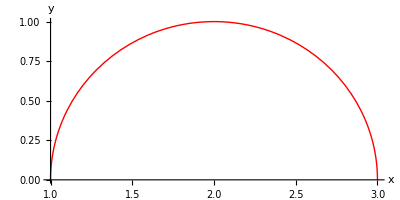

∫_c 1/(z-2)ⅆz =ⅈ π

```mathematica
z[t_]:=2+Exp[I*t];
Print["The parametrization of the semicircle C is given by"];
Print["C:z(t)=",z[t],", 0≤t≤π"];
Print["The plot of the semicircle C is given by the figure"]
ParametricPlot[{Re[z[t]],Im[z[t]]},{t,0,Pi},PlotStyle->{Thick,Red},AxesLabel->{x,y}]
f[z_]:=1/(z-2);
Print["∫_c 1/(z-2)ⅆz =",ComplexExpand[Integrate[f[z[t]]z'[t],{t,0,Pi}]]]
```